```mathematica
σ1[b_,x_]:= 1/(1+E^(-2b x))
σ2[b_,x_]:=1/2(1+(b x)/(√(1+(b x)^2)))
σ3[b_,x_]:=If[x>1/b,1,If[x<-1/b,0,(b x+1)/2]]
σ4[b_,x_]:=If[x>π/(2b),1,If[x<-π/(2b),0,(1+Sin[b x])/2]]
```

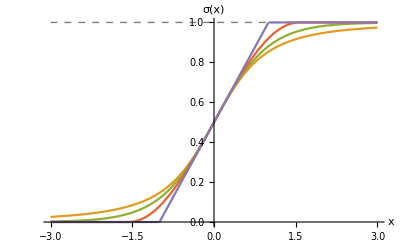

```mathematica
Plot[{1,σ2[1,x],σ1[1,x],σ4[1,x],σ3[1,x]},{x,-3,3},PlotRange->All,AxesLabel->{Style["x",FontSize->18],Style["σ(x)",FontSize->18]},
BaseStyle->{FontWeight->"Plain",FontSize->16},PlotStyle->{{Thin,Gray,Dashed},Default,Default,Default,Default}]
```

```mathematica
Simplify[{D[σ1[b,x],x],D[σ2[b,x],x],D[σ3[b,x],x]}]
```

{(2 b ⅇ^(2 b x))/((1+ⅇ^(2 b x))^2),b/(2 (1+b^2 x^2)^(3/2)),Piecewise[{{b/2, 1/b≥x&&1/b+x≥0}, {0, True}}]}

```mathematica
sl=Solve[σ2[b,x]==y,x]
```

{{x→-(ⅈ (-1+2 y))/(b √y √(-4+4 y))},{x→(ⅈ (-1+2 y))/(b √y √(-4+4 y))}}

```mathematica
PowerExpand[Simplify[Simplify[D[σ2[b,x],x]] /. sl[[1]]]]
```

4 b (y-y^2)^(3/2)

```mathematica
Clear[y,x];ssl=Simplify[DSolve[{y'[x]==4b(y[x](1-y[x]))^(3/2),y[0]==1/2},y,x]]
```

{{y→Function[{x},(1+b^2 x^2-b x √(1+b^2 x^2))/(2 (1+b^2 x^2))]},{y→Function[{x},(1+b^2 x^2+b x √(1+b^2 x^2))/(2 (1+b^2 x^2))]}}

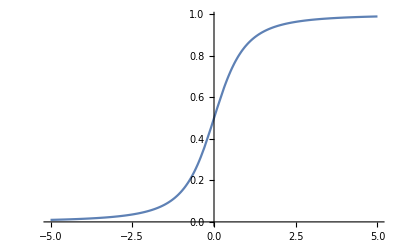

```mathematica
Plot[Re[1-y[x]/.ssl[[1]] /.b->1],{x,-5,5}]
```

```mathematica
sla=Solve[σ1[b,x]==y,x] /.C[1]->0
```

{{x→Log[-y/(-1+y)]/(2 b)}}

```mathematica
Simplify[D[σ1[b,x],x]/.sla]
```

{-2 b (-1+y) y}

```mathematica
ndsl=NDSolve[{y'[x]==(4y[x](1-y[x]))^1.2,y[0]==1/2},y,{x,0,3}]
```

{{y→InterpolatingFunction[…]}}

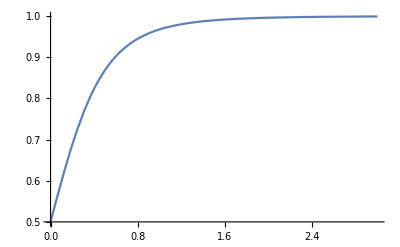

```mathematica
Plot[Re[y[x]/.ndsl],{x,0,3},PlotRange->All]
```

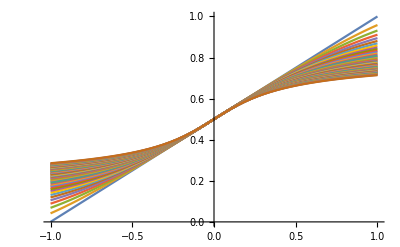

```mathematica
fvt=Table[{ndsl=NDSolve[{y'[x]==0.5(4y[x](1-y[x]))^α,y[0]==1/2},y,{x,-1,1}];Re[y[x]/.ndsl]},{α,0,10,0.2}];
Plot[fvt,{x,-1,1},PlotRange->{{-1,1},{0,1}}]
```